Determine when the free-space solution to the diffusion equation with gaussian IC stops being 0 at boundary.

Define gaussian.

```mathematica
f[x_,t_,𝒟_,σ_,L_]:=1/(√(2π(2 𝒟 t+σ^2)))Exp[-(x-L/2)^2/(2(2𝒟 t +σ^2))]
```

```mathematica
f[0,t,𝒟,σ,L]
```

(ⅇ^(-L^2/(8 (2 t 𝒟+σ^2))))/(√(2 π) √(2 t 𝒟+σ^2))

Plot where it intersects machine epsilon.

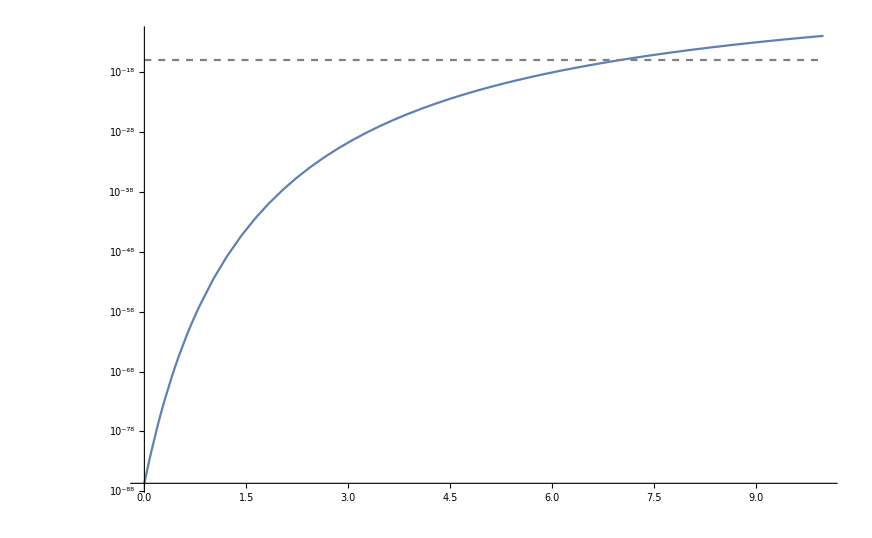

```mathematica
Show[LogPlot[f[0,t,0.02,0.25,10],{t,0,10}],LogPlot[10^-16,{t,0,10},PlotStyle->Directive[Gray,Dashed]]]
```

Solve for time when gaussian becomes nonzero at boundary.

```mathematica
FindRoot[f[0,t,0.01,0.25,10]==$MachineEpsilon,{t,5}]//Values//First
```

14.4072